# Chapter 8 Exploration and Transformation of Data

So far we have examined techniques for handling data when we believe the following:

1. The data are modeled by a linear relationship, especially a straight line or curve.

2. The data are modeled by a nonlinear relationship, such as a Gaussian.

3. The data are “smooth” in some sense and/or can be described by some nonparametric fit.

4. The data contain “outliers” which should be suppressed in the context of the analysis.

Sometimes we are confronted by data about which we have no knowledge of the relations that may exist within it, or what sort of values might be expected for some relation or model. This chapter discusses some techniques for exploring such a data set. As we shall see, sometimes the exploration leads us to transform the original data into other forms.

Also included in Section 8.3 is a discussion of the EDA function FindPeaks briefly introduced in Chapter 5.

Section 8.4 discusses a convenience routine FitPeaks which bundles FindPeaks and EDAFindFit together for fitting reasonably simple spectra to Gaussians or Lorentzians; the routine is named FitPeaks. Also discussed in this section is another convenience routine FitExponent to automatically fit data to exponentials of the form y = A ⅇ^(B x) without introducing the biases inherent in simple linearization schemes.

Mathematica is a particularly rich environment for exploratory data analysis, and there is a growing literature on using it for this purpose. This chapter does not attempt to repeat the material readily available elsewhere. Some references are listed in Section 8.4.

## 8.1 Graphical Exploration

As we have seen repeatedly in the previous chapters, graphs are invaluable in data analysis. Experimental Data Analyst (EDA) supplies some specific graphics functions, such as ShowLinearFit discussed in Chapter 4. EDA also supplies some general purpose graphical functions that supplement the standard graphics routines of Mathematica, and those functions are described in this section.

### 8.1.1 EDAListPlot

The EDA function EDAListPlot was briefly introduced in Chapter 1. Here we review and extend that introduction.

Internally, EDAListPlot used the built-in ListPlot for data without errors and ErrorListPlot from the ErrorBarPlots package for data with errors. The advantage of EDAListPlot is that it reocgnizes data in the EDA format and automatically invokes the appropriate function.

```mathematica
Needs["EDA`"]
```

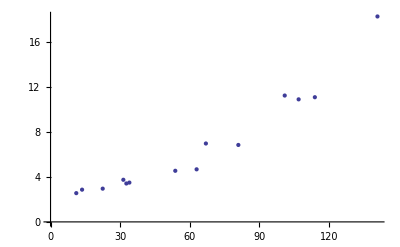

```mathematica
EDAListPlot[GanglionData]
```

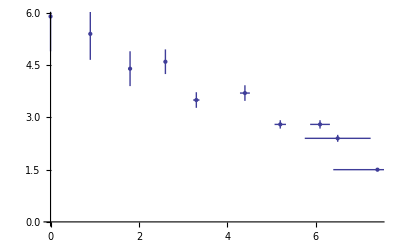

```mathematica
EDAListPlot[PearsonYorkData]
```

EDAListPlot can also handle more than one data set in a single plot.

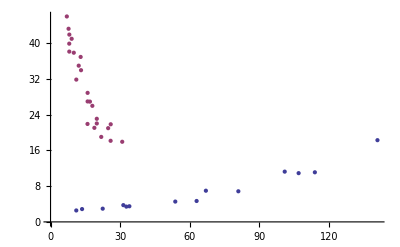

```mathematica
EDAListPlot[GanglionData, InterneuronData]
```

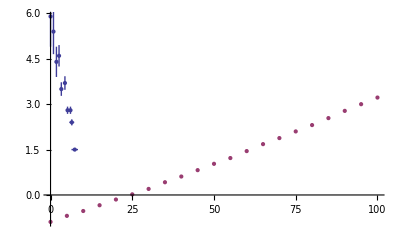

```mathematica
EDAListPlot[PearsonYorkData, ThermocoupleData]
```

However, all datasets must either have no explicit erorrs or must all have explicit errors.

```mathematica
EDAListPlot[GanglionData, PearsonYorkData]
```

EDAListPlot::mixedform: The datasets are not of the same type.

$Failed

### 8.1.2 BoxPlot

The box plot, sometimes called the “box and whisker plot”, is a way of visualizing distributions of data. We will illustrate with some data taken by Darwin in 1878.

```mathematica
Exit
```

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Darwin]
```

LoadData::name: Loading: CrossFertilizedData
and SelfFertilizedData

```mathematica
?CrossFertilizedData
```

CrossFertilizedData is the height of 15 Zea Mays plants that were
	cross-fertilized, measured in inches. The data was taken by Darwin
	in 1878.

```mathematica
?SelfFertilizedData
```

SelFertilizedData is the height of 15 Zea Mays plants that were
	self-fertilized, measured in inches. The data was taken by Darwin
	in 1878.

The data are some of the most analyzed ever, largely in pedagogical contexts. We form histograms of the two data sets using Mathematica’s built-in Histogram function.

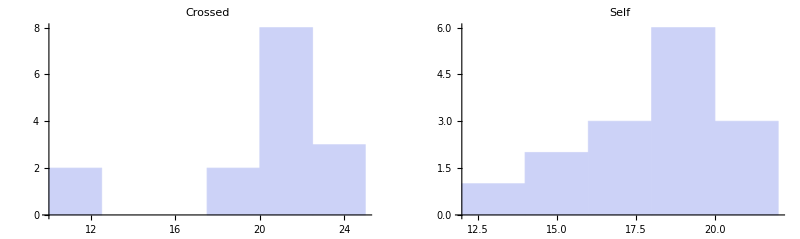

```mathematica
Show[GraphicsRow[{Histogram[CrossFertilizedData,5, PlotLabel->"Crossed",DisplayFunction->Identity],Histogram[SelfFertilizedData,5, PlotLabel->"Self",DisplayFunction->Identity]}],DisplayFunction->$DisplayFunction]
```

This seems to indicate that the cross-fertilized plants are somewhat larger.

The statistical measures, after some digging, seem to indicate the same.

```mathematica
myReport[data_] := Print[{{"Mean", Mean[data]}, {"HarmonicMean", HarmonicMean[data]},{"Quartiles", Quartiles[data]},{"StandardDeviation", StandardDeviation[data]},{"Skewness", Skewness[data]}}//TableForm]
```

```mathematica
myReport[CrossFertilizedData]
```

Mean | 20.1917
HarmonicMean | 19.337
Quartiles | 19.4375
21.5
22.125
StandardDeviation | 3.61695
Skewness | -1.55367

```mathematica
myReport[SelfFertilizedData]
```

Mean | 17.575
HarmonicMean | 17.3256
Quartiles | 16.3125
18.
18.625
StandardDeviation | 2.05168
Skewness | -0.718077

However, the EDA function BoxPlot shows the effect of fertilization clearly.

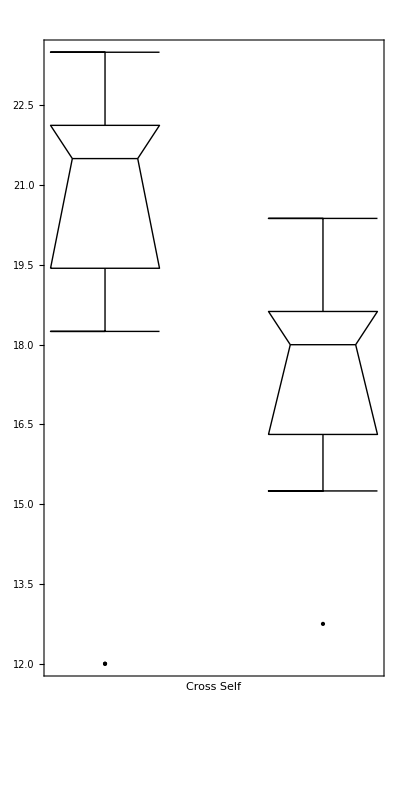

```mathematica
BoxPlot[{CrossFertilizedData,SelfFertilizedData},AspectRatio->2,FrameTicks -> {None, Automatic}, FrameLabel -> "Cross\t\t\tSelf"]
```

The “waist” in each box (which is actually two joined trapezoids) is the median of the data, the “shoulders” are at the upper quartile, and the “hips” are at the lower quartile. The vertical lines from the shoulders and hips extend to the maximum/minimum values of the data which are less/greater than the cutoffs; the cutoffs are the upper/lower quartiles plus or minus 3/2 of the height of the box, respectively. Any data that are represented as a point in the box plot is outside the cutoffs; there is one such datum in each of the data sets shown above.

Darwin threw out the data from Pot #1, which are the first three data points out of 15 for each sample; one of the plants died, another was diseased, and a third never grew to full height although a cause was not identified. The histograms and descriptive statistics are not very helpful in seeing the effect of throwing out this data.

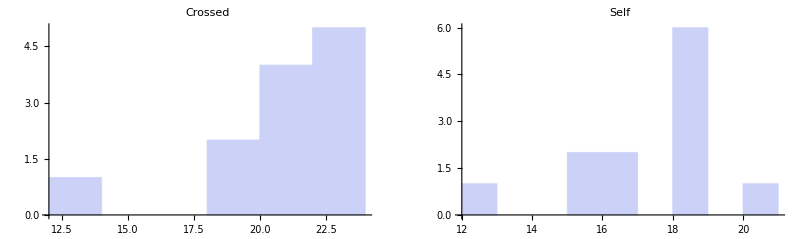

```mathematica
Show[GraphicsRow[{Histogram[Take[CrossFertilizedData,-12],5, PlotLabel->"Crossed",DisplayFunction->Identity],Histogram[Take[SelfFertilizedData,-12],5,PlotLabel->"Self",DisplayFunction->Identity]}],DisplayFunction->$DisplayFunction]
```

```mathematica
myReport[Take[CrossFertilizedData,-12]]
```

Mean | 20.5313
HarmonicMean | 19.9267
Quartiles | 19.75
21.5625
22.125
StandardDeviation | 3.06099
Skewness | -1.94287

```mathematica
myReport[Take[SelfFertilizedData,-12]]
```

Mean | 17.1563
HarmonicMean | 16.922
Quartiles | 15.875
18.
18.5
StandardDeviation | 1.97867
Skewness | -0.797908

Using BoxPlot makes the comparison easy.

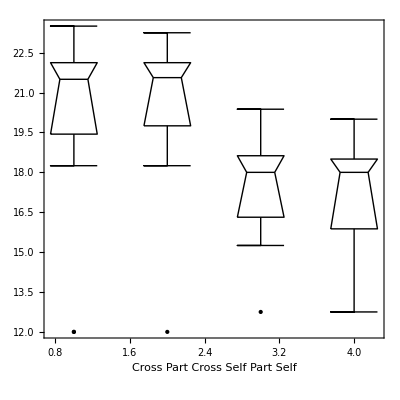

```mathematica
BoxPlot[{CrossFertilizedData,Take[CrossFertilizedData,-12],SelfFertilizedData,Take[SelfFertilizedData,-12]}, AspectRatio -> 1,FrameLabel -> "Cross\t\tPart Cross\t\tSelf\t\tPart Self"]
```

In particular, since the box plot is based on robust descriptors of data such as the median and the quartiles, the effect of throwing out the three data points is shown to have virtually no effect on our conclusions regarding the fertilization’s influence on plant growth.

Internally, BoxPlot uses the graphics primitives Point and Line. Options given to BoxPlot are passed to the Show function, and the defaults differ from the defaults for Show only in setting Frame -> True and PlotRange -> All.

### 8.1.4 Log and Log-Log Plots

The standard add-on Mathematica package Graphics`Graphics` contains the functions LogListPlot and LogLogListPlot to do log plots and log-log plots. As a convenience, EDA includes two routines that take data formatted for EDA, reformats it, and passes it to the functions in Graphics`Graphics`. The convenience routines are named EDALogListPlot and EDALogLogListPlot. Any explicit errors in the data are ignored and all options are passed to LogListPlot or LogLogListPlot.

Reference: Wolfram Research, Mathematica 4.0 Standard Add-on Packages.

### 8.1.5 Summary of General Purpose EDA Graphics Routines

```mathematica
Needs["EDA`"]
```

```mathematica
Information["EDAListPlot",LongForm->False]
```

EDAListPlot[data] produces a plot of data. It determines 
		if there are errors associated with the data points, and
		if so displays them also. EDAListPlot[data1, data2, ... ]
		displays multiple data sets. Internally, EDAListPlot uses
		the built-in ListPlot and ErrorListPlot[] from the
		standard ErrorBarPlots` package.

```mathematica
TableForm[Options[EDAListPlot]]
```

AlignmentPoint→Center
AspectRatio→1/GoldenRatio
Axes→True
AxesLabel→None
AxesOrigin→Automatic
AxesStyle→{}
Background→None
BaselinePosition→Automatic
BaseStyle→{}
ClippingStyle→None
ColorFunction→Automatic
ColorFunctionScaling→True
ColorOutput→Automatic
ContentSelectable→Automatic
CoordinatesToolOptions→Automatic
DataRange→Automatic
Epilog→{}
ErrorBarFunction→Automatic
Filling→None
FillingStyle→Automatic
Frame→False
FrameLabel→None
FrameStyle→{}
FrameTicks→Automatic
FrameTicksStyle→{}
GridLines→None
GridLinesStyle→{}
ImageMargins→0.
ImagePadding→All
ImageSize→Automatic
ImageSizeRaw→Automatic
InterpolationOrder→None
Joined→False
Joined→True
LabelStyle→{}
MaxPlotPoints→∞
Mesh→None
MeshFunctions→{#1&}
MeshShading→None
MeshStyle→Automatic
Method→Automatic
PlotLabel→None
PlotMarkers→None
PlotRange→Automatic
PlotRangeClipping→True
PlotRangePadding→Automatic
PlotRegion→Automatic
PlotStyle→Automatic
PreserveImageOptions→Automatic
Prolog→{}
RotateLabel→True
Ticks→Automatic
TicksStyle→{}
DisplayFunction:>$DisplayFunction
FormatType:>TraditionalForm
PerformanceGoal:>$PerformanceGoal

```mathematica
Information["BoxPlot",LongForm->False]
```

BoxPlot[{a1, a2, ..., aN}] displays statistics about {a1, a2, ..., aN}.
	The "box" spans the inner two quartiles, with an interior line
	at the median. Lines extend from the box to the minimum/maximum
	values which are greater/lesser than the cutoffs, respectively.
	The cutoffs are the lower/upper quartiles minus/plus 3/2 of the
	height of the box, respectively. Data outside the cutoffs are
	represented by points. BoxPlot[{{a1, ..., aN}, {b1, ..., bM},...}]
	displays boxplots for a, b, ... side by side. Optional final
	arguments to BoxPlot[] are passed to Show[].

```mathematica
TableForm[Options[BoxPlot]]
```

AlignmentPoint→Center
AspectRatio→Automatic
Axes→False
AxesLabel→None
AxesOrigin→Automatic
AxesStyle→{}
Background→None
BaselinePosition→Automatic
BaseStyle→{}
ColorOutput→Automatic
ContentSelectable→Automatic
CoordinatesToolOptions→Automatic
DisplayFunction:>$DisplayFunction
Epilog→{}
FormatType:>TraditionalForm
Frame→True
FrameLabel→None
FrameStyle→{}
FrameTicks→Automatic
FrameTicksStyle→{}
GridLines→None
GridLinesStyle→{}
ImageMargins→0.
ImagePadding→All
ImageSize→Automatic
ImageSizeRaw→Automatic
LabelStyle→{}
Method→Automatic
PlotLabel→None
PlotRange→All
PlotRangeClipping→False
PlotRangePadding→Automatic
PlotRegion→Automatic
PreserveImageOptions→Automatic
Prolog→{}
RotateLabel→True
Ticks→Automatic
TicksStyle→{}

```mathematica
?EDALogListPlot
```

EDALogListPlot[data] is a front end to ListLogPlot. 
		It takes data in the usual EDA format,
		reformats it, and passes it to ListLogPlot.

```mathematica
?EDALogLogListPlot
```

EDALogLogListPlot[data] is a front end to ListLogLogPlot.
		It takes data in the usual EDA format, reformats it, and
		passes it to ListLogLogPlot.

## 8.2 Transforming Data

There are three similar reasons why one may wish to transform a data set. First, sometimes the data itself suggests a transformation. Second, it can happen that a model exists for the data, but the model is not formulated directly in terms of the variables of the data. Third, a transformation can sometimes point out hidden features of the data. In this section, we will examine these three related cases. No new functions from EDA are introduced in this section; rather, Mathematica built-in functions and EDA functions discussed previously are used to perform transformations of the data.

### 8.2.1 The Data Itself Suggests a Transformation

We begin by considering some data on the population of cities.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Population]
```

LoadData::name: Loading: PopulationData

```mathematica
?PopulationData
```

PopulationData is the population of the 10 largest cities
	of 16 countries as reported by the 1967 "World Almanac".
	The countries listed are, in order: Sweden, the Netherlands,
	Canada, France, Mexico, Argentina, Spain, England, Italy,
	West Germany, Brazil, the Soviet Union, Japan, the United
	States, India, and China. Populations are in 100,000s. The
	countries are sorted by the value of the median of the population.
	The data for each individual country is available as, for example,
	"SwedenData".

Using the BoxPlot function discussed in the previous section, we examine this data.

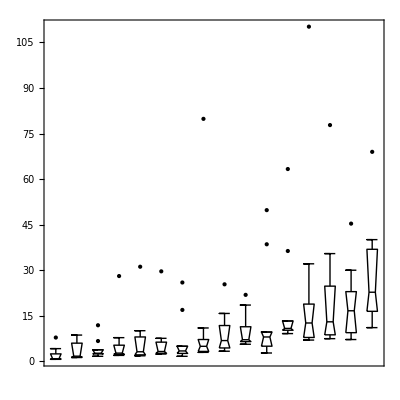

```mathematica
BoxPlot[PopulationData,FrameTicks->{None,Automatic}, AspectRatio -> 1]
```

Some of the features of the data include the fact that, with two exceptions, all countries’ city populations are skewed toward larger cities. We also see that for every country but one (the Netherlands) the biggest city is designated as an outlier.

The feature of the data seen above that will be of most concern here is the fact that as the median (the “level”) of the population increases, the height of the box (the “spread”) also tends to increase. In order to compare the data for the various countries, we will seek a transformation that minimizes the change in the spread with the level.

For this particular data, there is some theoretical justification for choosing a logarithmic transformation, since many models assume that populations tend to grow exponentially. We form the box plot for the logarithm of the populations.

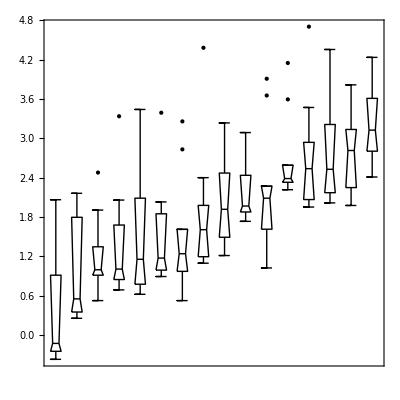

```mathematica
BoxPlot[Log[PopulationData],FrameTicks->{None,Automatic}, AspectRatio -> 1]
```

Even if we were ignorant of demography, we will show that the data itself suggests a logarithmic transformation.

Suppose that the spread is proportional to a power of the median.

spread = c * median^b

Take the logarithm of both sides.

Log[ spread ] = Log[ c ] + b * Log[ median ]

Thus, a fit of Log[spread] versus Log[median] to a straight line allows us to estimate b. Then we do a transformation of the data.

transf = original^(1 - b)

This transformation will, at least approximately, eliminate the dependence of spread on level.

In practice, we only estimate (1 - b), which leads to the following table.

```mathematica
TableForm[{{"b","Transformation"},"",{-2,"original^3"},{-1,"original^2"},{0,"original (No transformation)"},{0.5,"Sqrt[original]"},{1,"Log[original]"},{1.5,"1/Sqrt[original]"},{2,"1/original"}}]
```

b | Transformation
 | 
-2 | original^3
-1 | original^2
0 | original (No transformation)
0.5 | Sqrt[original]
1 | Log[original]
1.5 | 1/Sqrt[original]
2 | 1/original

This is often called Tukey’s “ladder of powers”.

The transformation Log[original] when (1 - b) is zero may seem to be artificial, but it is not. In fact, x^(1 - b) behaves much like the logarithm when (1 - b) is close to zero. For example, the derivative of Log[x] is 1/x, and the derivative of x^0.001 is proportional to x^-0.999.

When in doubt about what transformation to try, the logarithm is usually a good first choice. The reason is that often the factor we are trying to eliminate is multiplicative instead of additive, such as perhaps some percentage of the variable. A logarithmic transformation will give equal differences in the case of equal multiplicative factors.

Applying the ladder of powers to the population data, we first extract the quartiles.

```mathematica
q=Quartiles/@PopulationData
```

{{0.78,0.88,2.49},{1.42,1.735,6.02},{2.49,2.705,3.84},{2.33,2.74,5.35},{2.17,3.185,8.06},{2.69,3.275,6.35},{2.64,3.455,5.01},{3.3,4.985,7.22},{4.44,6.87,11.82},{6.53,7.15,11.42},{5.02,8.055,9.68},{10.27,10.87,13.32},{7.89,12.66,18.88},{8.76,13.045,24.79},{9.47,16.68,22.98},{16.5,22.785,36.92}}

The medians are the center value of each triple.

```mathematica
medians=(#1⟦2⟧&)/@q
```

{0.88,1.735,2.705,2.74,3.185,3.275,3.455,4.985,6.87,7.15,8.055,10.87,12.66,13.045,16.68,22.785}

We calculate the quartile spreads.

```mathematica
qspreads=(#1⟦3⟧-#1⟦1⟧&)/@q
```

{1.71,4.6,1.35,3.02,5.89,3.66,2.37,3.92,7.38,4.89,4.66,3.05,10.99,16.03,13.51,20.42}

Thus, we form a data set of { median, spread }.

```mathematica
mydata=Transpose[{medians,qspreads}];
```

We fit the logarithms to a straight line with the EDA LinearFit function; since mydata is not the normal type of experimental data the program was mainly designed for, we set the Reweight option to False.

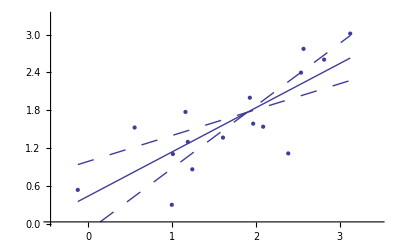

{a[0]→{0.44,0.55},a[1]→{0.7,0.29},SumOfSquares→3.46152,DegreesOfFreedom→14}

```mathematica
LinearFit[Log[mydata],{0,1},a,Reweight->False]
```

The slope is between 0.4 and 1.0. The latter suggests the logarithmic transformation we have already examined, while the former suggests a square-root transformation.

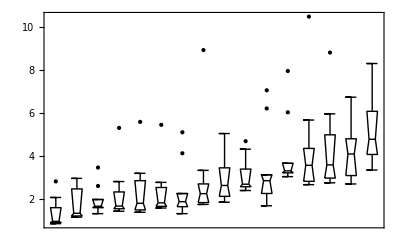

```mathematica
BoxPlot[√PopulationData,FrameTicks->{None,Automatic}]
```

This transformation also reduces the dependence of spread on the median, although perhaps not as well as the logarithmic one.

Although we have been dealing with transformations as a tool to enhance visual comparison, these sorts of transformations are sometimes necessary in order to use common confirmatory methods. For example, classical analysis-of-variance models assume constant variance within groups.

A similar example of when transformations can be required or preferred is illustrated by the ganglion data which we have already examined in Chapters 4, 6, and 7.

We will load the data and review the fit to a parabola which we have made to it.

```mathematica
LoadData[Ganglion]
```

LoadData::name: Loading: GanglionData

```mathematica
?GanglionData
```

GanglionData is data for the ratio of the central ganglion cell density
	to the peripheral density versus retinal area for 14 cat fetuses.
	The fetuses ranged in age from 35 to 62 days, and the retinal area
	is approximately monotonic in the age of the fetus. The data is from
	Barry Lia, Robert W. Williams, and Leo M Chalupa, Science 236, (1987)
	pg 848. The format of the data is {area, CP}, where area is in mm^2
	and CP is dimensionless.

Remember that CP denotes central to peripheral cell density ratio and area denotes retinal area.

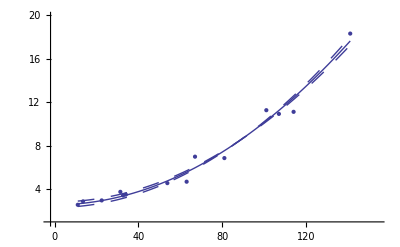

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12,Residuals→{{11.1,{-0.09,0.69}},{13.6,{0.17,0.69}},{22.5,{0.02,0.69}},{31.4,{0.44,0.69}},{32.7,{0.05,0.69}},{34.,{0.06,0.69}},{53.8,{-0.2,0.69}},{63.,{-0.88,0.69}},{67.,{1.02,0.69}},{81.,{-0.68,0.69}},{101.,{0.97,0.69}},{107.,{-0.32,0.69}},{114.,{-1.3,0.69}},{141.,{0.68,0.69}}}}

```mathematica
result=LinearFit[GanglionData,{0,2},a,ReturnResiduals->True]
```

We extract the residuals throwing away the errors.

```mathematica
residuals = Transpose[{First /@Partition[Flatten[Residuals /. result],3], Part[#,2]& /@ Partition[Flatten[Residuals /. result],3]}]
```

{{11.1,-0.09},{13.6,0.17},{22.5,0.02},{31.4,0.44},{32.7,0.05},{34.,0.06},{53.8,-0.2},{63.,-0.88},{67.,1.02},{81.,-0.68},{101.,0.97},{107.,-0.32},{114.,-1.3},{141.,0.68}}

We have also previously used the EDA function LoessFit to show that the average residuals for this fit are very close to zero.

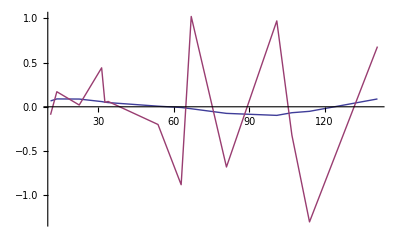

```mathematica
EDAListPlot[LoessFit[Residuals/.result,1,Points->13],residuals,Joined -> True,PlotLegend->{"LoessFit","Raw"}, PlotRange -> All]
```

However, the square root of the absolute values of the residuals is not constant but rather tends to increase. We form a level-spread data set, ignoring the errors in the residuals contained in result.

```mathematica
CPfitted=(2.56+0.000757 #1^2&)/@First/@GanglionData;
sqrtResiduals=√Abs[First/@Last/@(Residuals/.result)];
```

```mathematica
lsdata=Transpose[{CPfitted,sqrtResiduals}];
```

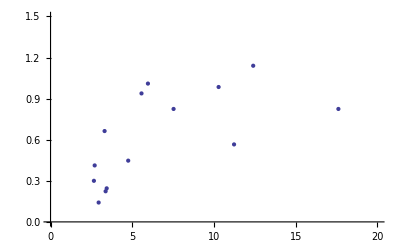

```mathematica
EDAListPlot[lsdata,PlotRange->{{0,20},{0,1.5}},AxesOrigin->{0,0}]
```

The details of why we take each data point to be the following are discussed in Section 8.2.1.1.

{fitted value of dependent variable,√Abs[residual]}

For now, we simply state that this is the equivalent of the {median, quartile spread} data set we formed earlier for the city population.

In attempting to compute confidence intervals for the results of the fit to the data using the standard Statistics`ConfidenceIntervals` package, for example, the technique used depends on whether or not the residuals increase or decrease with level. If the absolute values of the residuals depend on level it is called a “monotone” behavior. Eliminating monotone behavior by a transformation of the data gives a more reliable statistical result.

We fit the logarithm of the level-spread data to a straight line.

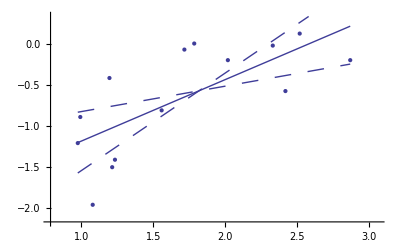

{a[0]→{-1.93,0.8},a[1]→{0.75,0.44},SumOfSquares→2.74984,DegreesOfFreedom→12}

```mathematica
LinearFit[Log[lsdata],{0,1},a,Reweight->False]
```

From Tukey’s ladder of powers, we can reasonably transform with Log[CP]or Sqrt[CP]. We form a data set in which we do the logarithmic transformation.

```mathematica
transfGanglionData=({#1⟦1⟧,Log[#1⟦2⟧]}&)/@GanglionData;
```

We fit to a line.

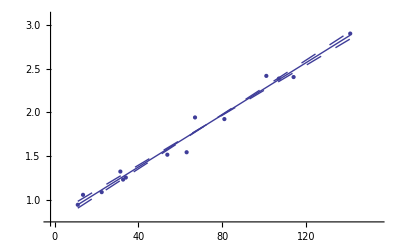

{a[0]→{0.774,0.046},a[1]→{0.01499,0.00063},PseudoErrorY→0.0933286,SumOfSquares→0.104523,DegreesOfFreedom→12,Residuals→{{11.1,{0.,0.093}},{13.6,{0.076,0.093}},{22.5,{-0.026,0.093}},{31.4,{0.077,0.093}},{32.7,{-0.035,0.093}},{34.,{-0.031,0.093}},{53.8,{-0.065,0.093}},{63.,{-0.175,0.093}},{67.,{0.165,0.093}},{81.,{-0.064,0.093}},{101.,{0.132,0.093}},{107.,{0.012,0.093}},{114.,{-0.076,0.093}},{141.,{0.019,0.093}}}}

```mathematica
newresult=LinearFit[transfGanglionData,{0,1},a,ReturnResiduals->True]
```

We form a level-spread data set analogous to the one before, again ignoring the errors in the residuals.

```mathematica
newresData=Transpose[{(0.77+0.015 #1&)/@First/@GanglionData,√Abs[First/@Last/@(Residuals/.newresult)]}];
```

Examination shows that we have effectively eliminated the monotone behavior of the residuals.

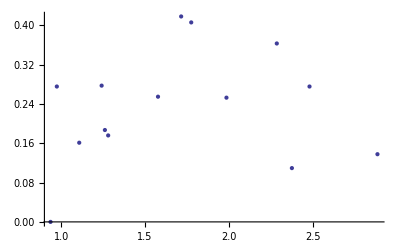

```mathematica
EDAListPlot[newresData]
```

Finally, in the fit of the original ganglion data to a parabola in Chapter 4, the data were reweighted using a statistical assumption, which is the default for LinearFit when there are no errors in the data. Although the result was fairly reasonable, we can now see that the fact that the residuals of that fit increase with the value of the dependent variable means that the reweight procedure is not entirely reasonable. For the transformed ganglion data transfGanglionData, however, it is reasonable.

We have been pushing this ganglion data pretty hard here and in previous chapters. Some problems inherent in many experiments, especially in the life sciences, are that variations in samples, inherent noise in the measurements, and limited sample sizes are common. Here we see problems in the fact that, for example, there is a triple of data points on the right that have almost the same value of the CP ratio for measurably different areas. Whether this triple is due to differences in the individual fetuses or difficulty in measurement is not certain, but it is not grounds for criticizing the experimenters. The existence of such features, however, means that any analysis of this data should be viewed skeptically.

That having been said, in the absence of a theoretical model for the way the CP ratios could be related to the retinal area, we can go a bit further with the result of this last fit to the data. We have used the data itself to make a model of the following form.

Log[ CP ] = a[0] + a[1]*area

Such a model can arise when the change in the CP ratio, call it Delta(CP) is proportional to the value of CP itself times the change in the area of the retina, Delta(area). Thus, the conclusion is that by transforming the data we have found a suggestion of a model for the growth of the retina.

#### 8.2.1.1 Level and Spread for Bivariate Data

When we examined the level and spread for the city population data, the level was chosen to be the median and the spread was chosen to be the quartile spread. These choices for data with only one coordinate, a “univariate” data set, are perfectly reasonable and natural.

When the data has two coordinates (“bivariate”) like the ganglion data, we made two decisions that may not be quite so obvious. First, we chose the level to be the fitted value of the dependent variable. Second, we chose the spread to be the square root of the absolute value of the residuals. In this section we discuss these decisions.

Regarding the level, imagine that the univariate city data were not sorted by the value of the medians.

```mathematica
randomorder={1,8,2,16,3,11,14,5,9,15,7,4,13,6,10,12};
```

```mathematica
randomData=Table[PopulationData⟦randomorder⟦i⟧⟧,{i,1,16}];
```

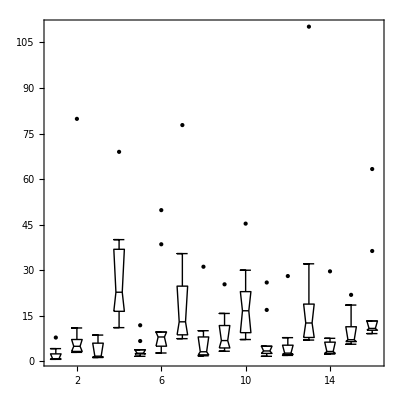

```mathematica
BoxPlot[randomData,FrameTicks->{{2,4,6,8,10,12,14,16},Automatic}, AspectRatio -> 1]
```

Further, imagine that we characterize each country’s data by its position in the list. Clearly, the “level” of each country is not that position. Similarly, for a bivariate data set, it is not the value of the independent variable that sets the level, but the value of the dependent variable.

Considering the “level” for a data set such as the Cobalt60Data we have examined in previous chapters may make this realization even clearer.

```mathematica
LoadData[Cobalt60]
```

LoadData::name: Loading: Cobalt60Data

```mathematica
?Cobalt60Data
```

Cobalt60Data is part of a cobalt-60 nuclear spectrum. The
	format is: {channel, counts}. The data was collected in the second-year
	Lab of the Department of Physics, University of Toronto with a NaI 
	scintillator and a PC-based multichannel analyzer running PC-MCA software 
	by David Harrison (1990, unpublished).

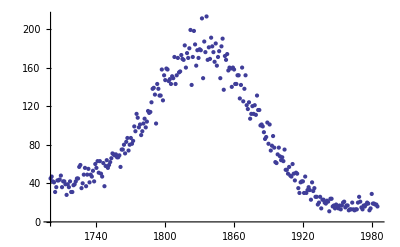

```mathematica
EDAListPlot[Cobalt60Data]
```

Clearly, in this case the level must be the value of the dependent variable, not the independent one.

To illustrate why we should use the fitted value of the dependent variable to measure the level instead of the experimental data value, we will repeat a couple of straight-line fits we performed earlier.

```mathematica
LoadData[Anscombe]
```

LoadData::name: Loading: AnscombeData[[i]], for i = 1,2,3,4

```mathematica
?AnscombeData
```

AnscombeData is a quartet of made-up data devised by F.J.
	Anscombe, American Statistician 27 (Feb. 1973), pg 17.
	All four data sets, AnscombeData[[1]], AnscombeData[[2]],
	AnscombeData[[3]], and AnscombeData[[4]], have almost identical
	averages and fit to almost identical straight lines. The format
	of each data set is {x, y}, where neither coordinate has units.

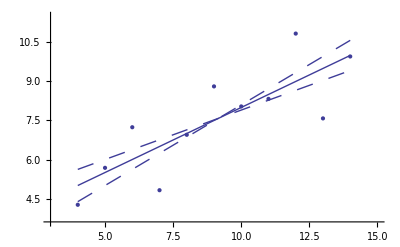

{a[0]→{3.,1.1},a[1]→{0.5,0.12},PseudoErrorY→1.2366,SumOfSquares→13.7627,DegreesOfFreedom→9,Residuals→{{4.,{-0.7,1.2}},{5.,{0.2,1.2}},{6.,{1.2,1.2}},{7.,{-1.7,1.2}},{8.,{0.,1.2}},{9.,{1.3,1.2}},{10.,{0.,1.2}},{11.,{-0.2,1.2}},{12.,{1.8,1.2}},{13.,{-1.9,1.2}},{14.,{0.,1.2}}}}

```mathematica
ansc1=LinearFit[AnscombeData⟦1⟧,{0,1},a,ReturnResiduals->True,ResidualPlacement->None]
```

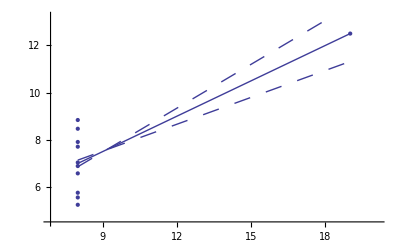

{a[0]→{3.,1.1},a[1]→{0.5,0.12},PseudoErrorY→1.2357,SumOfSquares→13.7425,DegreesOfFreedom→9,Residuals→{{8.,{-1.8,1.2}},{8.,{-1.4,1.2}},{8.,{-1.2,1.2}},{8.,{-0.4,1.2}},{8.,{-0.1,1.2}},{8.,{0.,1.2}},{8.,{0.7,1.2}},{8.,{0.9,1.2}},{8.,{1.5,1.2}},{8.,{1.8,1.2}},{19.,{0.,1.2}}}}

```mathematica
ansc4=LinearFit[AnscombeData⟦4⟧,{0,1},a,ReturnResiduals->True,ResidualPlacement->None]
```

We form level-spread data sets using the values of y for the level.

```mathematica
try1=Transpose[{Last/@AnscombeData⟦1⟧,√Abs[Last/@(Residuals/.ansc1)]}];
```

```mathematica
try4=Transpose[{Last/@AnscombeData⟦4⟧,√Abs[Last/@(Residuals/.ansc4)]}];
```

These two sets look about the same, despite the fact that the data that generated them are so very different.

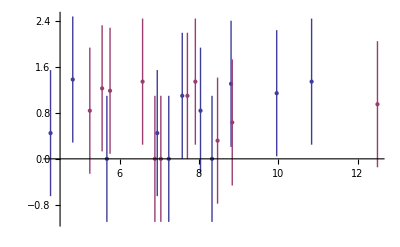

```mathematica
EDAListPlot[try1,try4, PlotRange -> All]
```

However using a “better” level, the fitted values of y, makes the differences between the two sets obvious.

```mathematica
better1=Transpose[{(3+0.5 #1&)/@First/@AnscombeData⟦1⟧,√Abs[Last/@(Residuals/.ansc1)]}];
```

```mathematica
better4=Transpose[{(3+0.5 #1&)/@First/@AnscombeData⟦4⟧,√Abs[Last/@(Residuals/.ansc4)]}];
```

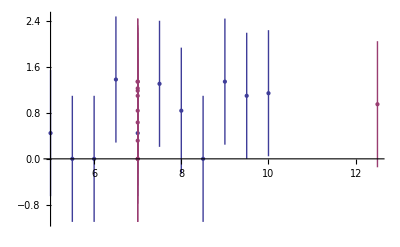

```mathematica
EDAListPlot[better1,better4, PlotRange -> All]
```

The reason for using the square root transformation on the residuals is more heuristic: absolute residuals are almost always skewed toward large values and the square root transformation reduces the asymmetry. In addition, since the level is the fitted values, in some sense information about the residuals is contained in both axes of the plot. Experience has shown that in terms of a first estimate of a data transformation using the ladder of powers, the square root of the residuals does a better job of suppressing both the asymmetry in the absolute residuals and the fact that we are “double-counting” the residuals in the plot.

### 8.2.2 Transforming to Match a Model

Often we have a data set whose variables do not directly correspond to a model to which we will try to fit the data. For example, in the next subsection we will take some pressure-volume data of the form {p, v} and fit it to a model based on Boyle’s law, which states that the pressure times the volume is a constant. Thus, we will form a new data set of {p, 1/v} and fit it to a straight line.

The powerful list manipulation facilities of Mathematica, plus the techniques for combining data which has experimental errors already described in Chapter 3, often makes this type of transformation easy to do.

However, one aspect of this type of transformation that can be important is that it can introduce biases in the results of the analysis. Those biases will be the principle focus of this subsection.

We will illustrate with some made-up, noisy data that obeys the following relation.

y = a ⅇ^-bx

We will generate the noise with a Monte-Carlo technique.

```mathematica
noise={};
Module[{x,num},SeedRandom[1234];num=0;While[num<100,x=RandomReal[{-4,4}];If[RandomReal[]≤ⅇ^(-x^2/2),noise=Append[noise,x];num++;];];];
```

The noise contains 100 numbers, distributed as a Gaussian with mean of zero and standard deviation of 1.

```mathematica
Needs["EDA`"]
```

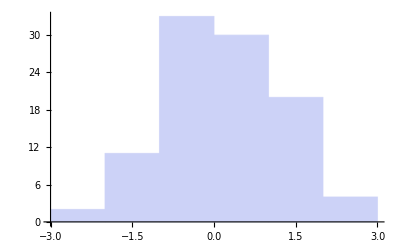

```mathematica
Histogram[noise]
```

We will add the noise to the dependent variable for 100 generated data points.

```mathematica
Module[{x,a=32750,b=0.1},mydata=Table[{x,a Exp[-b x]+noise⟦x⟧},{x,100}];];
```

We can fit this using the EDA function EDAFindFit.

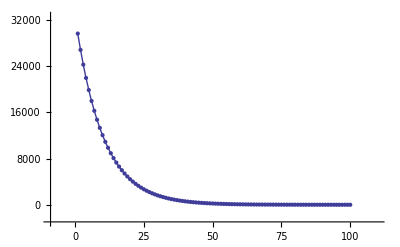

{a→{32750.2,0.7},b→{0.0999991,2.9×10^-6},SumOfSquares→107.632,DegreesOfFreedom→98}

```mathematica
EDAFindFit[mydata,a Exp[-b x],x,{{a,32500},{b,0.09}}]
```

This fit matches the data very nicely.

We take the logarithm of the model.

Log[y] = Log[a] - b*x

This transformation is sometimes called linearization. A fit of Log[y] versus x will give a straight line of slope b and intercept Log[a]. We form a transformed data set of {x, Log[y]}.

```mathematica
transf=({#1⟦1⟧,Log[#1⟦2⟧]}&)/@mydata;
```

We fit this transformed data to a straight line.

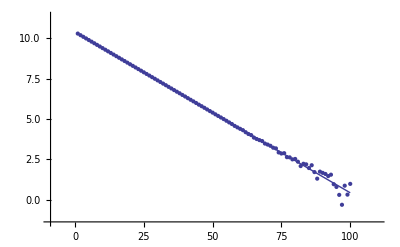

{a→{32300.,6500.},b→{-0.0995,0.0035},SumOfSquares→2.52475,DegreesOfFreedom→98}

```mathematica
EDAFindFit[transf,Log[a]+b x,x,{{a,32700},{b,0.09}}]
```

In the previous subsection, we found that transforming can eliminate monotone behavior in the residuals. Since here the original data mydata by construction has random residuals which are independent of the level (that is the value of y) it is not surprising that transforming the data creates a monotone behavior in the residuals: their absolute value increases as the level decreases.

The nature of these residuals is reflected in the large error for the estimate of a. And the estimate of a, although falling within 32750+6500 and 32750-6500, has been systematically shifted away from the right number. This shift is a parameter bias introduced by the transformation. The estimate of b is not biased by this transformation.

In general, calculating the amount of bias introduced by transforming the data is complicated. Thompson calculates the bias for a logarithmic transformation when the noise in the original data is proportional to the level, which is not the case here.

Section 8.4 discusses a convenience routine, FitExponent, that automatically fits data to the form y = A ⅇ^(B x) by estimating parameter values by linearization of the model and using LinearFit and then using those estimates to fit to the exponential with EDAFindFit.

Reference: William J. Thompson, Computing for Scientists and Engineers (Wiley, 1992), Section 6.5.

In conclusion, it is important to keep in mind that arbitrary transformations of data can have unintended side effects by introducing biases in parameter estimates. The material in this subsection underlines the importance of transforming data to eliminate monotone behavior in residuals when fitting models.

### 8.2.3 Finding Hidden Features of the Data

We load and examine some data on pressure and volume of a fixed quantity of dry air.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Boyle]
```

LoadData::name: Loading: BoyleData

```mathematica
?BoyleData
```

BoyleData is based on data for testing Boyle's law taken by a 
	first-year student at the University of Toronto in the Department of
	Physics undergraduate laboratories in 1983. A fixed quantity of dry air
	at room temperature had its pressure and volume measured for a
	number of different values of the pressure. The format of each
	data point is { {p, errp}, {v, errv} }, where p and errp are
	the value and error in the pressure, measured in cm of Hg, and v
	and errv are the value and error in the volume, measured in cm^3.

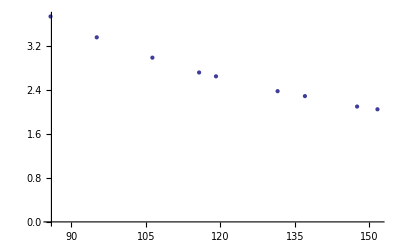

```mathematica
EDAListPlot[BoyleData]
```

Boyle’s law states that the pressure times the volume is a constant number. Thus, a fit of pressure versus 1/volume should be a straight line. We transform to a data set of {1/v, p} and try the fit. First we extract the pressure and volume data.

```mathematica
p=First/@BoyleData;
```

```mathematica
v=Last/@BoyleData;
```

We wish to propagate the errors in the volume when we form the inverse of v, so we will use the Data construct introduced in Section 3.3.1.1.

```mathematica
vinv=1/Data[v]/.Data->Identity;
```

Now we form a new data set.

```mathematica
mydata=Transpose[{vinv,p}];
```

We fit to a straight line.

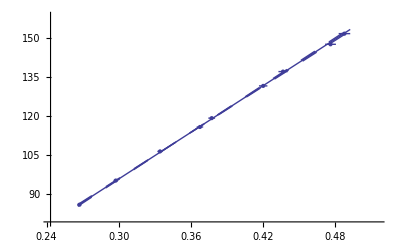

{a[0]→{6.1,1.3},a[1]→{298.7,3.7},ChiSquared→1.19108,DegreesOfFreedom→7}

```mathematica
LinearFit[mydata,{0,1},a]
```

Note that everything about this fit looks fine except perhaps a small inverse parabolic shape to the residuals. But a little further thought will indicate that all is not well with this data. Since the independent variable is 1/v, the intercept corresponds to the pressure when the volume is infinite, so it should be zero. We repeat the fit, forcing the intercept to be zero.

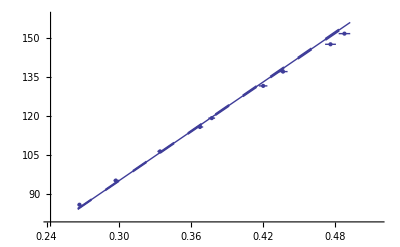

{a[1]→{316.57,0.76},ChiSquared→22.0791,DegreesOfFreedom→8}

```mathematica
LinearFit[mydata,{1},a]
```

This fit is awful.

One of the difficulties here is that the errors in the data are sufficiently small that we are having some difficulty seeing exactly what is going on. But if Boyle’s law is true, then the value of pressure times volume should be exactly the same within errors for each datum. We form the product, including errors, and examine the result.

```mathematica
pv=TimesWithError[p,v];
```

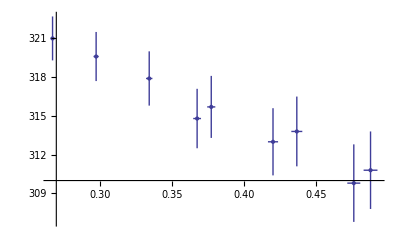

```mathematica
EDAListPlot[Transpose[{vinv,pv}], PlotRange -> All]
```

The air sample for which this data is taken is inside a vertical glass tube. The top of the tube has been closed, and mercury fills the bottom part of the tube. The volume of air is deduced from the length of the tube containing the sample . However, the top of the tube has been closed in a sloppy fashion so the experimenter must guess the position of the top. If the guess is poor, a systematic error in the volume will be generated that can lead to data such as seen in the above plot. (The sloppiness in the closing of the top of the tube is by design for this experiment in a teaching laboratory.)

We fit this data to a line.

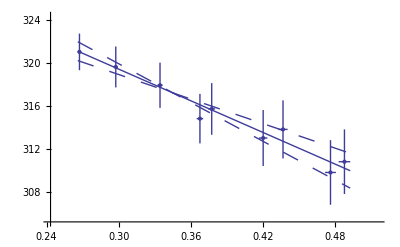

{a[0]→{334.1,3.8},a[1]→{-49.,11.},ChiSquared→0.660224,DegreesOfFreedom→7}

```mathematica
LinearFit[Transpose[{vinv,pv}],{0,1},a]
```

The intercept corresponds to the value of pressure times volume when the inverse of the volume is zero. This is the value for infinite volume, when this systematic effect should become zero.

We can find the correction needed for the volume data by realizing that there is some value for c for which the following is true.

p * (v + c) = 334

We rearrange the equation.

c=334/p-v

The mean over all the data points is given by the following.

```mathematica
Mean[First/@(334/p-v)]
```

0.155441

Thus, the volumes are systematically too low by .155 cm^3. We add this figure to the volume data.

```mathematica
newv=({First[#1]+.155,Last[#1]}&)/@v;
```

Next we recalculate the inverse of the volume.

```mathematica
newvinv=1/Data[newv]/.Data->Identity;
```

Finally, we repeat the fit of p versus the inverse of v to a line with zero intercept.

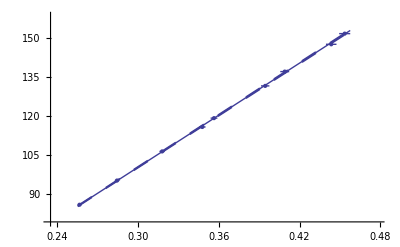

{a[1]→{334.,0.76},ChiSquared→0.833274,DegreesOfFreedom→8}

```mathematica
LinearFit[Transpose[{newvinv,p}],{1},a]
```

Thus, after transforming the data based on graphical exploration and with an understanding of the actual apparatus used to take the data, we have confirmed that Boyle’s law is consistent with this experiment. We also note that the student has apparently overestimated the experimental errors since the ChiSquared per DegreesOfFreedom is small.

## 8.3 Estimating Parameters for Peaks

As mentioned in Section 5.1.2, there is no known software that can find peaks in a spectrum and estimate parameters for them as well as a human expert. As also discussed there, the most promising software for doing this task may be based on neural networks; the computational requirements of these networks and the fact that this is still an active area of research means that EDA does not attempt to supply such technology at this time.

However, in the case of fairly simple spectra EDA does supply a function (FindPeaks) which can often find and estimate peaks well enough for the EDA function EDAFindFit to successfully find a fit to the data. This section discusses that FindPeaks function. The following section discusses a convenience function that bundles FindPeaks and EDAFindFit together into a FitPeaks function that automatically fits to reasonably simple spectra.

One basic idea used by FindPeaks is that the peak position corresponds to a minimum in the second derivative of the spectrum provided that the second derivative is negative, and the width of the peak is measured by where the second derivatives are equal to zero.

The other basic idea of FindPeaks involves the question of the function of which we should be taking the second derivatives. As discussed in some detail in Section 6.1.5, a reasonable choice is to form an InterpolationFunction, take its derivative and smooth the result using the EDA function SmoothData. We then interpolate the smoothed first derivatives, take its derivative, and smooth the result to get the second derivatives.

We will first load and examine some data we looked at in Chapter 5.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Cobalt60]
```

LoadData::name: Loading: Cobalt60Data

```mathematica
?Cobalt60Data
```

Cobalt60Data is part of a cobalt-60 nuclear spectrum. The
	format is: {channel, counts}. The data was collected in the second-year
	Lab of the Department of Physics, University of Toronto with a NaI 
	scintillator and a PC-based multichannel analyzer running PC-MCA software 
	by David Harrison (1990, unpublished).

```mathematica
EDAListPlot[Cobalt60Data]
```

-Graphics-

We use FindPeaks on this data.

```mathematica
FindPeaks[Cobalt60Data]
```

{Bkgd[0]→175.331,Bkgd[1]→-0.079386,Amplitude[1]→145.612,CenterValue[1]→1830.,PeakWidth[1]→96.,PeaksFound→1}

Note that FindPeaks has returned the intercept Bkgd[0] and slope Bkgd[1] of a linear background term. It has also estimated the peak to have an amplitude Amplitude[1] of 146.924 and center value CenterValue[1] of 1830. PeakWidth[1] is the estimated full width of the peak. It is estimated from the values where the second derivatives of the peak are equal to zero. Also returned is PeaksFound, which is the number of peaks found in the data.

FindPeaks can accept a second argument specifying a peak shape.

```mathematica
result=FindPeaks[Cobalt60Data,Gaussian]
```

{Model→ⅇ^(-(IndependentVariable-CenterValue[1])^2/(2 EDASigma[1]^2)) Amplitude[1]+Bkgd[0]+IndependentVariable Bkgd[1],EDAParameters→{{Bkgd[0],175.331},{Bkgd[1],-0.079386},{Amplitude[1],145.612},{CenterValue[1],1830.},{EDASigma[1],48.}},PeaksFound→1}

Now FindPeaks has returned a Model, which in this case is a function of parameters Bkgd[0], Bkgd[1], and a Gaussian with amplitude Amplitude[1], center value CenterValue[1], standard deviation Sigma[1], and independent variable IndependentVariable. Also, FindPeaks has returned a rule for EDAParameters specifying the names and initial guesses of the parameters. Thus, the result from FindPeaks is in a form suitable for giving to the EDA function EDAFindFit.

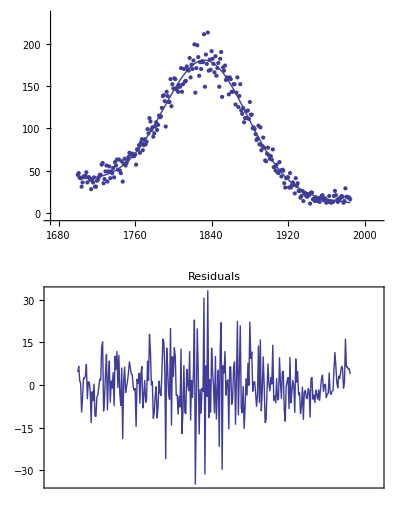

{Bkgd[0]→{201.5,1.6},Bkgd[1]→{-0.09556,0.00087},Amplitude[1]→{154.03,0.17},CenterValue[1]→{1833.51,0.054},EDASigma[1]→{43.499,0.069},SumOfSquares→23500.7,DegreesOfFreedom→281}

```mathematica
EDAFindFit[Cobalt60Data,Model/.result,IndependentVariable,EDAParameters/.result]
```

FindPeaks can also try to estimate parameters and form a model assuming that the shape is a Lorentzian or Breit-Wigner.

```mathematica
FindPeaks[Cobalt60Data,Lorentzian]
```

{Model→Bkgd[0]+IndependentVariable Bkgd[1]+(FWHM[1] PeakArea[1])/(2 π ((IndependentVariable-CenterValue[1])^2+FWHM[1]^2/4)),EDAParameters→{{Bkgd[0],175.331},{Bkgd[1],-0.079386},{PeakArea[1],38031.9},{CenterValue[1],1830.},{FWHM[1],166.277}},PeaksFound→1}

Now the Model is a background plus a Lorentzian.

FindPeaks can find more than one peak in a data set. We will illustrate with some data we have already examined.

```mathematica
LoadData[MassSpec]
```

LoadData::name: Loading: MassSpecData

```mathematica
?MassSpecData
```

MassSpecData is mass spectrometer data for two isotopes,
	taken by Dr. Alex Young, Dept. of Chemistry, Univ. of Toronto
	(1995, unpublished). The format is {amu,ions}, where amu
	is the mass, in atomic mass units, and ions is the number of
	ions.

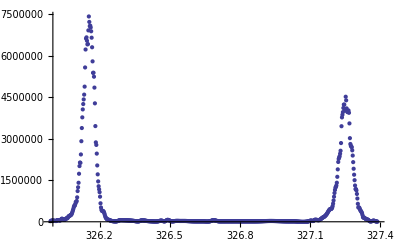

```mathematica
EDAListPlot[MassSpecData,PlotRange->All]
```

FindPeaks has a EDAShowProgress option which, if set to True, displays graphs illustrating its progress.

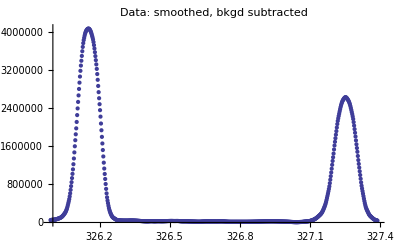

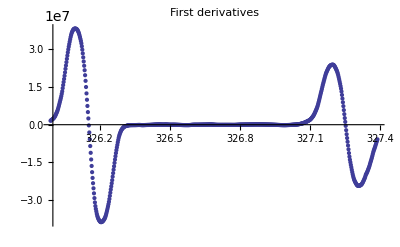

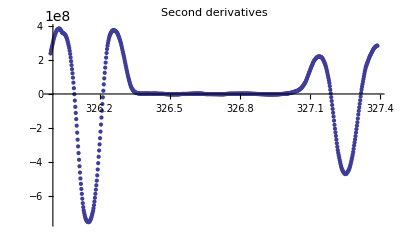

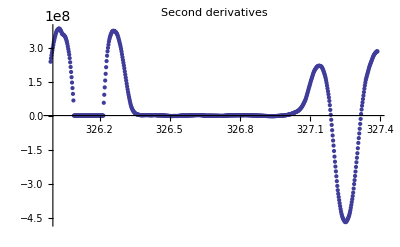

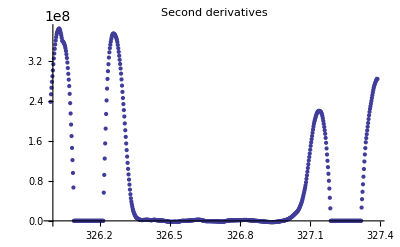

{Amplitude[1]→6.92172×10^6,CenterValue[1]→326.152,PeakWidth[1]→0.124,Amplitude[2]→4.32655×10^6,CenterValue[2]→327.254,PeakWidth[2]→0.128,PeaksFound→2}

```mathematica
FindPeaks[MassSpecData,EDAShowProgress->True]
```

The first graph shows the data after smoothing and subtracting the background, if any. Then the graph of the first derivatives is displayed, followed by the graph of the second derivatives. The minimum negative value in this graph is used to locate and characterize the first peak. Then all the second derivatives for this peak are set to a small positive number, as shown in the second graph labeled “Second derivatives”, and the new minimum negative value is used to find the second peak. The values for this peak are set to a small positive number, as shown in the final graph, and FindPeaks concludes there are no more peaks to be found.

As our final example, we will generate some made-up data for two Gaussians with significant overlap and with some noise.

```mathematica
SeedRandom[1234];
mydata=Table[{x,Gaussian[x,10,5,2]+Gaussian[x,8,10,2]}+RandomReal[{0,0.1}],{x,0,20,0.1}];
```

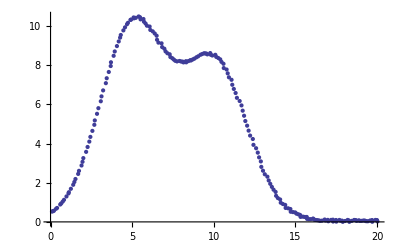

```mathematica
EDAListPlot[mydata]
```

Note for future reference that the first Gaussian has amplitude = 10, center = 5, and sigma = 2, while the second Gaussian has amplitude = 8, center = 10, and sigma = 2.

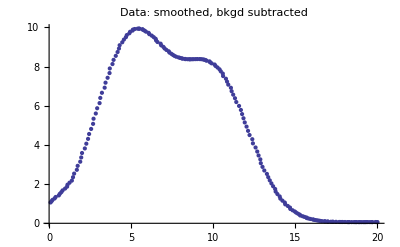

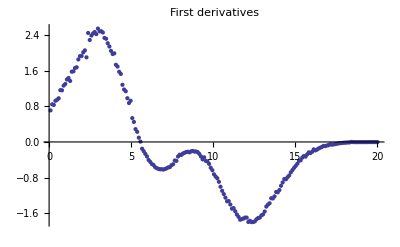

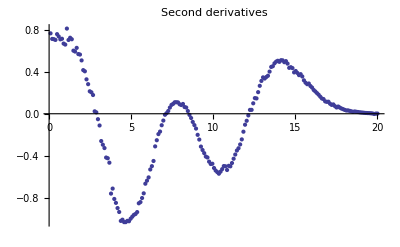

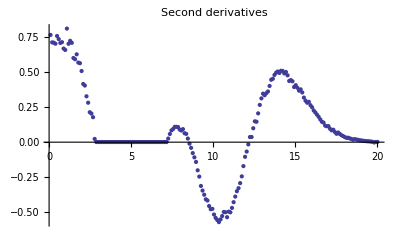

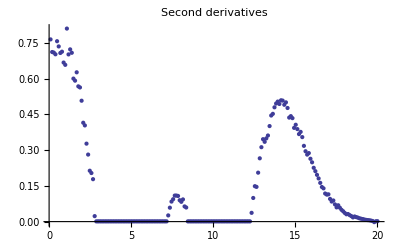

{Model→ⅇ^(-(IndependentVariable-CenterValue[1])^2/(2 EDASigma[1]^2)) Amplitude[1]+ⅇ^(-(IndependentVariable-CenterValue[2])^2/(2 EDASigma[2]^2)) Amplitude[2],EDAParameters→{{Amplitude[1],9.93742},{CenterValue[1],4.57358},{EDASigma[1],2.09343},{Amplitude[2],8.28267},{CenterValue[2],10.3554},{EDASigma[2],1.84421}},PeaksFound→2}

```mathematica
result=FindPeaks[mydata,Gaussian,EDAShowProgress->True]
```

The estimated parameter values are fairly close, and certainly close enough for EDAFindFit to complete their determination,

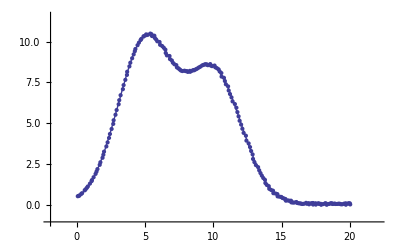

{Amplitude[1]→{10.02,0.31},CenterValue[1]→{5.04,0.15},EDASigma[1]→{2.01,0.11},Amplitude[2]→{8.04,0.31},CenterValue[2]→{10.05,0.19},EDASigma[2]→{2.02,0.13},SumOfSquares→0.686653,DegreesOfFreedom→195}

```mathematica
EDAFindFit[mydata,Model/.result,IndependentVariable,EDAParameters/.result]
```

### 8.3.1 Summary of FindPeaks

```mathematica
Information["FindPeaks",LongForm->False]
```

FindPeaks[data] finds peaks in "data" and returns Amplitude[i],
	CenterValue[i], and PeakWidth[i] for each of the i peaks found.
	FindPeaks[data, shape] finds peaks in "data" and returns a 
	model for the peaks assuming the shape of the peaks is given
	by "shape", and also returns initial parameter estimates as
	"EDAParameters". FindPeaks[data, None] is a synonym for FindPeaks[data].
	Other allowed values for "shape" are BreitWigner, Gaussian, or
	Lorentzian. For each of these the model and parameters may be
	passed to the EDAFindFit routine.

```mathematica
TableForm[Options[FindPeaks]]
```

FindBkgd→Automatic
MaximumPeaks→5
EDAShowProgress→False

```mathematica
Information["FindBkgd",LongForm->False]
```

FindBkgd is an option for FindPeaks. If set to Automatic (the
	default), a linear background will be used and returned provided
	such a background accounts for over 2% of the sum of all values of
	the dependent variable in the data. If set to None, no background
	term is used or returned by FindPeaks.

```mathematica
Information["MaximumPeaks",LongForm->False]
```

MaximumPeaks is an option for FindPeaks that controls the maximum
	number of peaks in the data that it will attempt to find.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

```mathematica
Information["Amplitude",LongForm->False]
```

Amplitude[i] is the amplitude of the ith peak found by FindPeaks.

```mathematica
Information["Bkgd",LongForm->False]
```

Bkgd is a symbol used by FindPeaks to represent the background in
	the spectrum. When a background is found, FindPeaks returns the
	symbol Bkgd[0] as the intercept and the symbol Bkgd[1] as the slope.

```mathematica
Information["CenterValue",LongForm->False]
```

CenterValue[i] is the center of the ith peak found by FindPeaks.

```mathematica
Information["FWHM",LongForm->False]
```

FWHM[i] is the full width at half maximum of the ith peak found
	by FindPeaks.

```mathematica
Information["IndependentVariable",LongForm->False]
```

IndependentVariable is the symbol used by FindPeaks to represent
	the independent variable.

```mathematica
Information["Model",LongForm->False]
```

Model is the model constructed by FindPeaks.

```mathematica
Information["EDAParameters",LongForm->False]
```

EDAParameters is the symbol used by FindPeaks to represent the
	names and initial values of the parameters.

```mathematica
Information["PeakArea",LongForm->False]
```

PeakArea[i] is the area under the ith peak found by FindPeaks.

```mathematica
Information["PeaksFound", LongForm -> False]
```

PeaksFound is the number of peaks found by FindPeaks.

```mathematica
Information["PeakWidth",LongForm->False]
```

PeakWidth[i] is the width of the ith peak found by FindPeaks.
	It is the width from the points where the second derivative is
	zero. For a Guassian shape, this corresponds to 2 times the
	standard deviation. For a Lorentzian shape, it corresponds to
	the full width at half maximum divided by Sqrt[3].

```mathematica
Information["EDASigma",LongForm->False]
```

EDASigma[i] is the standard deviation of the ith peak found by
	FindPeaks.

## 8.4 FitPeaks and FitExponent

As a convenience, EDA bundles up some other EDA functions into routines to handle specific tasks. This section discusses two of them, FitPeaks and FitExponent.

### 8.4.1 FitPeaks

The idea behind FitPeaks is discussed in the previous section: use FindPeaks to estimate the number and values of the peaks in a spectrum and then use those estimates for EDAFindFit to fit the data.

By default, FitPeaks fits to a Gaussian model. We shall use it to fit to mydata, which was first constructed in the previous section. Recall that the data contains two overlapping Gaussians.

```mathematica
Needs["EDA`"]
```

```mathematica
SeedRandom[1234];
mydata=Table[{x,Gaussian[x,10,5,2]+Gaussian[x,8,10,2]}+RandomReal[{0,0.1}],{x,0,20,0.1}];
```

```mathematica
EDAListPlot[mydata]
```

-Graphics-

```mathematica
FitPeaks[mydata]
```

-Graphics-

{Amplitude[1]→{10.02,0.31},CenterValue[1]→{5.04,0.15},EDASigma[1]→{2.01,0.11},Amplitude[2]→{8.04,0.31},CenterValue[2]→{10.05,0.19},EDASigma[2]→{2.02,0.13},SumOfSquares→0.686653,DegreesOfFreedom→195}

As seen above, by default FitPeaks fits to Gaussians. A PeakShape option may be set to Lorentzian, in which case that is the shape used for the fit. All other options given to FitPeaks are passed to FindPeaks or EDAFindFit as appropriate.

### 8.4.2 FitExponent

As discussed in Section 8.2.2, fitting to an exponential y = A ⅇ^(B x) by linearization to Log[y] = Log[A] + B × x introduces biases in the parameters. However, fitting to the full exponential often requires that we have at least an approximate idea of the values of the parameters A and B. The FitExponent function uses the fact that the biases introduced by linearization are often fairly small, so estimates of the parameter values found through a linear fit may then be used for the full nonlinear one.

In Section 8.2.2 we constructed mydata, which is a noisy exponential with A equal to 32750 and B equal to 0.10.

```mathematica
noise={};
Module[{x,num},SeedRandom[1234];num=0;While[num<100,x=RandomReal[{-4,4}];If[RandomReal[]≤ⅇ^(-x^2/2),noise=Append[noise,x];num++;];];];
```

```mathematica
Module[{x,a=32750,b=0.1},mydata=Table[{x,a Exp[-b x]+noise⟦x⟧},{x,100}];];
```

```mathematica
Needs["EDA`"]
```

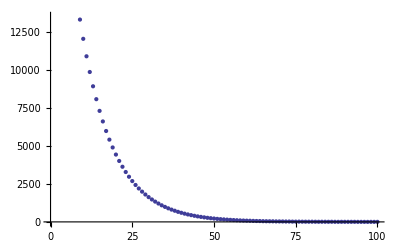

```mathematica
EDAListPlot[mydata]
```

We fit the data to an exponential.

```mathematica
FitExponent[mydata]
```

-Graphics-

{A→{32750.2,0.7},B→{-0.0999991,2.9×10^-6},SumOfSquares→107.632,DegreesOfFreedom→98}

Any options given to FitExponent are passed to EDAFindFit, which actually performs the fit.

## 8.5 References

As mentioned at the beginning of this chapter, there is a growing literature on using Mathematica in ways particularly appropriate for the topics of this chapter. The first subsection below lists some of these titles.

The second subsection below refers to a cross section of the literature on exploratory data analysis and transformation techniques.

Both lists are to be viewed as a selection, and readers may have personal favorites that do not appear below.

### 8.5.1 References to Mathematica

Alfred Riddle and Samuel Dick, Applied Electronic Engineering with Mathematica (Addison-Wesley, 1995). Although tied to electronics, much of the analysis discussed here has a much wider applicability than just in that field

William T. Shaw and Jason Tigg, Applied Mathematica: Getting Started, Getting It Done (Addison-Wesley, 1994). A collection of techniques that are of great value to any worker in the physical sciences or engineering

Stan Wagon, The Power of Visualization: Notes from a Mathematica Course (Front Range Press, 1994). A concise introduction to the topic of visualization of data

Tom Wickham-Jones, Mathematica Graphics: Techniques and Applications (TELOS/Springer-Verlag, 1994). Much of data exploration relies on graphical techniques, and this book provides both an introduction to Mathematica’s built-in graphics capabilities and rich extensions to those capabilities

### 8.5.2 References on Exploratory Data Analysis and Transformation

William S. Cleveland, Visualizing Data (AT&T Bell Labs, 1993). Although visualization is prominently featured here, there are also extensive discussions of fitting techniques, transformations, smoothing, etc.

David C. Hoaglin, Frederick Mosteller, and John W. Tukey, eds., Understanding Robust and Exploratory Data Analysis (John Wiley, 1983). A wide-ranging discussion of many of the topics of this chapter by experts

John W. Tukey, Exploratory Data Analysis (Addison-Wesley, 1977). Although the topics of this chapter go back to Descartes, this classic book caused an increased interest in them.